# Teoría de Autómatas y Lenguajes Formales

## MC-6003 II-2021 (Maestría en Ciencias de la Computación ITCR)

Profesor: Tomás de Camino Beck, Ph.D.

tomas.decamino@gmail.com

## Proyecto Final

El proyecto final, que tiene un valor de 200 puntos, consiste en el desarrollo de un proyecto libre, que incluya alguno de los temas visto en clase, o temas adicionales no cubiertos o relacionados a teoría de autómatas (o con teoría de computación).  El proyecto debe contener:

Debe ser desarrollando los puntos incluidos en este Notebook.

Debe contener la implementación en Mathematica de algún código, con detalles explicando su desarrollo y con al menos dos ejemplos.

Una vez encontrado un tema y desarrollado un código, hacer algún tipo de experimentación con el código, tal vez buscando alguna aplicación que pueda ser de interés.

Incluir al menos 5 referencias (indexadas)

## Introducción

Incluir una introducción tipo artículo científico del tema...

## Teoría

Descripción teórica del sistema a desarrollar...

## Desarrollo de código En Mathematica

En esta sección incluya el código desarrollado, con las explicaciones pertinentes...

## Ejemplos

Dos ejemplos de uso del código con explicación

##### MOST BASIC ENCRYPTION

Existen 2 personas que se comunican por mensajes encriptados, estos se ven un día en un parque y definen un numero como “public key” el cual será “7”, a partir de ahora estas personas nuncá más se volveran a ver y solamente se comunicaran por correo con los mensajes ya encriptados. Su mecanismo de encriptación funciona de la siguiente manera.

Su alfabeto es con carácteres de la “a...z”.

```mathematica
Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

La persona A, desea enviar el mensaje “secret” a la persona B, para esto usamos el public key como la variable que nos ayudará a encriptar. El funcionamiento de nuestro algoritmo consiste en movernos “k” espacios sobre el Alfabeto para cada letra, por ejemplo con k=7 la letra “e” pasará a ser la “l”, si el algoritmo llega a la ultima letra del alfabeto debe volver a empezar

```mathematica
validateKeyRange[alphabet_, publicKey_] := Module[{},
	If[publicKey > Length[alphabet], Mod[publicKey,Length[alphabet]], publicKey]
];

encryptorDecryptor[alphabet_,message_,publicKey_]:= Module[{chars, alphabetLength, currentPositions, newPositions, newMessage,validatedKey},
alphabetLength = Length[alphabet];
validatedKey = validateKeyRange[alphabet, publicKey];
chars = Characters[message];
currentPositions = Table[Position[alphabet,i],{i, chars}] //Flatten;
newPositions = Map[If[# + validatedKey > alphabetLength, # + validatedKey - alphabetLength, If[# + validatedKey <= 0, alphabetLength + (# + validatedKey),# + validatedKey]]&,currentPositions];
newMessage = FromLetterNumber[#]& /@ newPositions;
StringJoin[newMessage]
];

encryptorDecryptor[Alphabet[],"secret",4]
```

wigvix

Como podemos observar el mensaje encriptado queda como “wigvix”, la persona B recibirá este mensaje y si alguien lo intercepta en el camino no sabrá que significa a simple vista. La persona B deberá correr el algoritmo pero con el key en negativo para decifrar el mensaje.

```mathematica
encryptorDecryptor[Alphabet[],"wigvix",-4]
```

secret

Sin embargo este método es bastante fácil de crackear, incluso si el “public key” fuese un numero muy grande, un programador nada mas mediante fuerza bruta podría probar todos los k=1...1000.... y leer cuales producen un mensaje entendible y en adelante leer todos los mensajes de estas personas.

##### RSA ALGORITHM

El metodo de encriptacion RSA se basa en la factorización de numeros primos, por ejemplo si quisieramos encontar 2 numeros que multiplicados nos den de resultado el numero “8616460799” sería sumamente dificil lograrlo manualmente, por lo que necesitamos escribir un programa para lograrlo, pero que pasaría si encontramos numeros lo suficientemente grandes como para que incluso una computadora tarde demasiado (anos) en encontrarlos.

Mediante este metodo tendremos tanto un “public key” como “private key”, y los generaremos de la siguiente manera, usando los siguientes pasos.

Paso 1 : Seleccionamos dos numeros primos en este caso serán p=2 y q=7.

```mathematica
p= 2; q=7;
```

Paso 2 : Obtenemos el producto de estos 2 numeros y lo llamaremos “N1”

```mathematica
N1 = p * q
```

14

Paso 3 : Obtenemos “T” usando Euler Totient

```mathematica
T = (p - 1) * (q - 1)
```

6

Paso 4 : Necesitamos encontrar 2 numeros “e” y “d”. que cumplan “e*d mod T = 1”. e = encryption number y d = decryption number. Para esto debemos definir ciertas reglas.

• e debe ser menor a T.

• e deber primo relativo/coprime con T

```mathematica
encryptionNumber[t1_]:= NestWhile[# - 1 &,t1 - 1,CoprimeQ]

e = encryptionNumber[T]
```

5

Paso 5 debemos encontrar “d” que cumpla “e*d mod T = 1”.

```mathematica
decryptionNumber[e1_,t1_]:= Module[{d},
	d = e1 + 1;
	While[Mod[e1 * d, t1]!= 1, Nothing; d++];
	d
];
decryptionNumber[e,T]
```

11

Habiendo obtenido el numero encriptador y el decriptador hacemos lo siguiente :

Publicamos a todos los usuarios el Public Key el cual será (e,N) = (5,14)

Guardamos nuestro Private Key el cual será (d, N) = (11,14)

```mathematica
publicKey = {5,14};
privateKey = {11,14};
```

Supongamos que ahora quiero enviar a otra persona el mensaje “b”, esta otra persona solo conoce el Public Key y tiene su propio Private Key. Para hacer el envió definimos la función de encriptado, la cual esta dada por char ^ e mod N. El resultado es 4 y lo pasamos a letras.

```mathematica
encryptDecryptMessage[message_, publicKey_] := FromLetterNumber[Mod[LetterNumber[message]^publicKey[[1]],publicKey[[2]]]];
encryptDecryptMessage["b", publicKey]
```

d

Enviamos el mensaje encriptado, y el receptor deber desencriptarlo usando char ^ d mod N

```mathematica
encryptDecryptMessage["d", privateKey]
```

b

El metodo anterior usa primos muy pequenos para construir los keys, para poder aceptar alfabetos grandes con todos los simbolos debemos hacer una mejor solución de primos, para esto tenemos los estandares RSA-#. A continuación extenderemos un poco más la funcion de encriptado y decriptado para trabajar con strings con mas simbolos.

```mathematica
p = 11777623253100600606475568688692467522395803125194264009546341998455853099782265804864870878594598047222934141798969832793441585484966407147720677990883619;
q = 12353978300203236372526910502422393557961726275268960264014521143951779860477853396347304933752339630927134439217791364721884908085632288618105974588440853;
N1 = p * q;
T = (p - 1) * (q - 1);
encrypt = encryptionNumber[T];
decrypt= PowerMod[encrypt,-1,T];
publicKey = {encrypt,N1};
privateKey = {decrypt,N1};
encryptBigMessage[message_, key_] := Module[{numericValue},
(* Using ASCII codes we convert to a numeric value the string *)
numericValue = FromDigits[ToCharacterCode[message], 256];
(* char ^ e mod N *)
PowerMod[numericValue, key[[1]], key[[2]]]
];
newMessage = encryptBigMessage["Hello I am just testing some text!", publicKey]
```

59607645092781653589099679087771742070416182499401866716863715610607712243501964550361632134740688016289300758552320975252864383432953318744156366305020329903680400614155550164031019317742819781975817233011194603370402021844816987155430618740945616946960234351300260162952953978575770419813241556230126621952

```mathematica
decryptBigMessage[numericEncryption_, key_] := Module[{numericValue},
(* char ^ d mod N *)
numericValue = PowerMod[numericEncryption, key[[1]], key[[2]]];
FromCharacterCode[IntegerDigits[numericValue, 256]]
];
decryptBigMessage[newMessage, privateKey]
```

Hello I am just testing some text!

## Experimentación

Con el código desarrollado aplique a algún ejemplo que puede ser de interés, o realice algún tipo de experimentación. Cómo ejemplo pueden pensar en explorar todas las máquinas de Turing con ciertas características, y determinar cuantas se detienen en un tiempo determinado....  O utilizar un algoritmo genético para evolucionar una MT o autómata... (el cielo es el límite)

Tome toda la libertad de consultar al profesor si quiere ver algunas ideas de que puede hacer

Audio Original

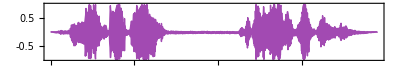

Generando el audio encriptado

Audio encriptado creado exitosamente!

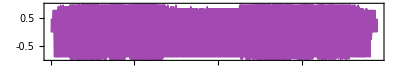

El audio encriptado ha sido exitosamente exportado

Momento de desencriptar el audio

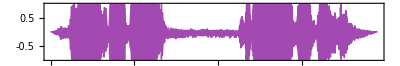

Audio desencriptado exitosamente

```mathematica
(* Definition of keys *)
Nvalue = 9516311845790656153499716760847001433441357;
publicKey = {65537,Nvalue};
privateKey = {5617843187844953170308463622230283376298685,Nvalue};

(*Definimos el path donde se encuentra el archivo*)
audioPath = "C:\\Users\\Andrey\\Desktop\\Automatas\\love.wav";
(*Cargamos un audio*)
Print["Audio Original"]
audio = Audio[File[audioPath]]
AudioPlot[audio]
(*Obtenemos el sample rate*)
sampleRate = Import[audioPath,"SampleRate"];
(*Obtenemos los datos del audio*)
data = AudioData[audio,"SignedInteger32"];

Print["Generando el audio encriptado"]
(*Encriptamos los valores*)
encryptedValues = Map[Map[encryptBigMessage[ToString[#], publicKey]&,#]&, data];

Print["Audio encriptado creado exitosamente!"]
(*Creamos un audio con los datos encriptados y lo exportamos*)
encryptedAudio = Audio[ListPlay[encryptedValues,SampleRate->sampleRate]]
AudioPlot[encryptedAudio]
Export["C:\\Users\\Andrey\\Desktop\\Automatas\\encrypted.wav",encryptedAudio];
Print["El audio encriptado ha sido exitosamente exportado"]

Print["Momento de desencriptar el audio"]
(*Desencriptamos los datos del audio encriptado*)
decryptedValues = Map[Map[ToExpression[decryptBigMessage[#, privateKey]]&,#]&, encryptedValues];
decryptedAudio = Audio[ListPlay[decryptedValues,SampleRate->sampleRate]]
AudioPlot[decryptedAudio]
Print["Audio desencriptado exitosamente"]
```

```mathematica
(* Definition of keys *)
p = 127;
q = 2;
Nvalue = p * q;
T = (p - 1) * (q - 1);
encrypt = encryptionNumber[T];
decrypt= decryptionNumber[encrypt,T];
publicKey = {encrypt,Nvalue};
privateKey = {decrypt,Nvalue};

img = Image[-Graphics-]
imgData = ImageData[img,"byte"];

(*Encriptamos los valores*)
encryptedValues = Map[Map[Map[encryptBigMessage[ToString[#], publicKey]&,#]&,#]&, imgData];
Image[encryptedValues, "byte"]
```

-Graphics-

-Graphics-

## Resultados

Muestre resultado de experimentación...

## Comentario Final y Trabajo Futuro

Comentarios finales y que se podría desarrollar

## Referencias

Al menos 5 referencias de revistas indexadas o libros

https://www.ripublication.com/gjpam16/gjpamv12n4_73.pdf

https://www.iosrjournals.org/iosr-jece/papers/Vol9-Issue1/Version-4/N09146973.pdf

https://www.ijareeie.com/upload/2014/may/50_Image.pdf

https://citeseerx.ist.psu.edu/viewdoc/download?doi=10.1.1.695.6887&rep=rep1&type=pdf

file:///C:/Users/Andrey/Downloads/259-Article%20Text-2725-2-10-20200617.pdf

http://azadproject.ir/wp-content/uploads/2013/12/2012-O23-Implementation-of-RSA-Algorithm-for-Speech-Data-Encryption-and-Decryption.pdf

https://arxiv.org/ftp/arxiv/papers/1509/1509.04387.pdf

https://github.com/nicholasbennet/audiorsa

https://github.com/sumitrj/RSA-Audio-Encryption-and-Decryption

https://github.com/sumitrj/RSA-Audio-Encryption-and-Decryption/blob/master/RSA%20-%20Audio%20implementation.ipynb

https://www.acadpubl.eu/hub/2018-118-21/articles/21c/63.pdf

https://issuu.com/ijtsrd.com/docs/136_image_cryptography_using_rsa_algorithm